Growth and spreading of topics on inSpireHEP/arXiv.org

Oliveri Roberto

Boyer Mark

Université Libre de Bruxelles (ULB), Brussels, Belgium

Most representative image

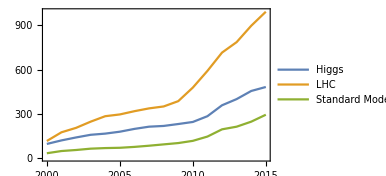
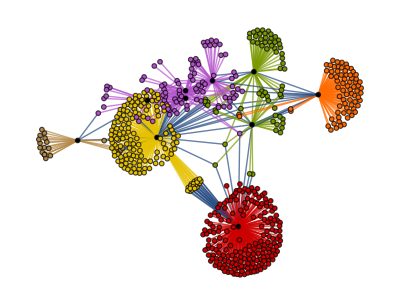

Abstract

GOAL OF THE PROJECT: 
The project has a twofold goal. Given a keyword representing a scientific topic (e.g., entanglement, gravitational waves, etc...), we compute the number of occurrences of the keyword that appears in the abstracts of papers in a given time interval and we study how papers about a specific topic are related to each other by analyzing the corresponding citations. In particular, we construct the citation graph associated to the topic and we display its time evolution.

SUMMARY OF WORK: 
As a preliminary step, we download an updated snapshot of record metadata in JSON format containing information about one million of papers posted on inSpireHEP. After adjusting the database to our purposes, we collect the abstracts year by year. The first goal is reached by using the built-in function StringCount, which counts how many times the keyword appears in the abstracts within a given time interval. Then we chart the occurrences by using DateListPlot and few examples of keyword search are shown. The second goal is achieved by selecting those papers concerning the chosen topic and by associating each of these papers to their list of citations. We construct the corresponding citation graph and highlight the communities by centrality-based clustering criterion. We emphasize those papers whose position is relevant for the topology of the graph. Finally, we introduce a further time selection of papers (in addition to the topic selection) in order to display the time evolution of the graph.

RESULTS AND FUTURE  WORK: 
In this project, we defined a search engine that charts occurrences of any keyword in the abstracts of papers posted on inSpireHEP/arXiv.org. As an example, we studied the occurrences of “LHC” and “Higgs” from 1985 to 2015. As expected, the “LHC” occurrences increase after the first run in 2008 and the “Higgs” occurrences increase soon after the announcement of the Higgs boson discovery in 2012. Another result is to emphasize those papers about one specific chosen topic that play an important role in the structure of the citations graph, because of their high degree of centrality and not only because they are the most cited papers in the field. Future directions are to study the properties of the citation graph in detail.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

Here we show the growth of the citations graph of papers about the “BMS group”:

In this case, the vertex cut of the final stage of the graph evolution (right picture) is a paper by Ashtekar entitled “A unified treatment of null and spatial infinity in general relativity. I - Universal structure, asymptotic symmetries, and conserved quantities at spatial infinity”. It is depicted in green inside the yellow bubble.

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

#### Keyword search engine

Our first result has been to compute the number of occurrences of keywords that appears in the abstracts of papers in a given time interval. The user has two degrees of freedom in his search: the keyword and the time interval. The research engine is a useful analytical tool to show the trend of a topic in the time range. In the following, we present some representative examples.

The search engine for the keyword “Higgs” shows that the occurrences increase soon after the announcement of the Higgs boson discovery in 2012. This is evident from the following plot:

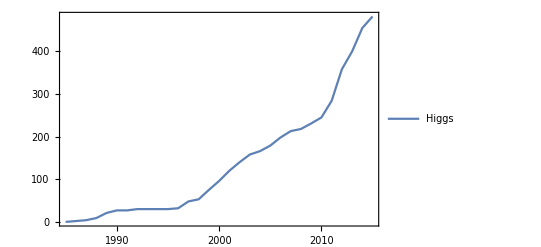

Another interesting fact that we can easily check is the correlation between the keywords “OPERA experiment” and “tachyon” from 2011, due to the wrong observation of muon neutrinos apparently traveling faster than the speed of light.

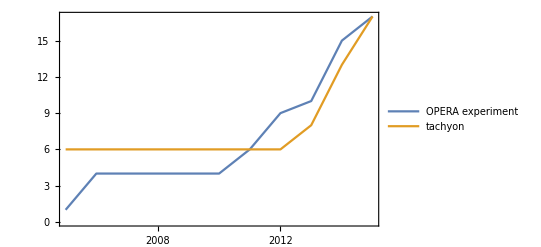

One more check is the correlation between “AdS/CFT” and “holographic principle” keywords, as shown below:

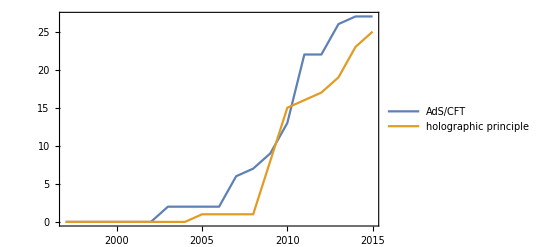

#### Citations graph and its growth

The citations graph is an useful tool to visualize the relations between papers concerning the same topic and to highlight hidden properties among them. 
To meet this aim, we construct the citations graph of those papers about the “BMS group”. Here is its visualization with graph communities in different colors:

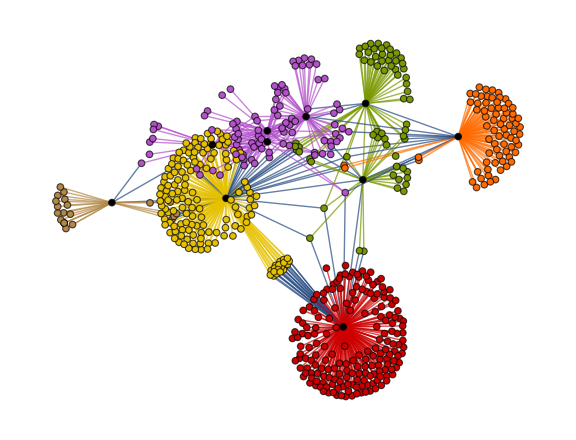

Within the whole set of papers about the “BMS group”, we might select the most cited papers. The number of citations is usually a reliable bibliometric quantity to evaluate the scientific quality of a paper. In the graph above, we highlighted the graph communities in different colors and the papers with the highest degree of centrality in black. The latter set of papers is a subset of the most cited papers and they play an important role in the topological structure of the graph. In other words, among the most cited papers, we introduce the centrality-based clustering criterion to select the most “important” papers. As an example, the black vertex inside the yellow community is the so-called vertex cut. A vertex cut is that vertex whose removal renders the graph disconnected. In this respect, that paper connects different communities (i.e., different sub-topics) and it represents a seminal paper in the field because it has a non trivial topological position in the graph. In the case at hand, it is the paper by Ashtekar entitled “A unified treatment of null and spatial infinity in general relativity. I - Universal structure, asymptotic symmetries, and conserved quantities at spatial infinity”.

It is also interesting to visualize the time evolution of the graph during a given time interval. To achieve this result, we need snapshots of the citations graphs year by year. In other words, we need to further select papers by date, in addition to the first selection by topic, and construct the corresponding graph. For the “BMS group” citation paper, we have the following growth:

Along the same lines, we studied the citations graph of papers about “AdS/CFT” in the time interval 1998 - 2008.
Here is a snapshot of the graph in 2001:

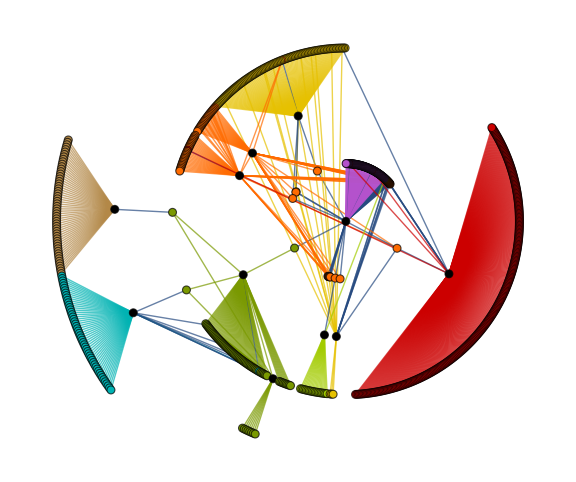

Here is a 3D visualization of the same graph:

-Graphics3D-

and its time evolution within the time interval:

Code

Provide one of:

Link to the GitHub: https://github.com/ROliveri89/WSS17_material

Explicit code: http://develop.wolframcloud.com/objects/da5a0d15-c5ff-40ce-b1aa-5b6890b13b1d

Written Content / Lesson Plans

Conclusions in Detail

In this project, we defined a search engine that charts occurrences of any keyword in the abstracts of papers posted on inSpireHEP/arXiv.org and constructed the corresponding citation graph and highlight the communities by centrality-based clustering criterion. Finally, we displayed the time evolution of the graph. Future directions of investigation require more complete database and a detailed analysis of the topological properties of the graph.

All Visualizations

For all the visualizations and animation, please read “Main Results in Detail”.

Here is the WordCloud of all authors involved in “AdS/CFT” up to 2015:

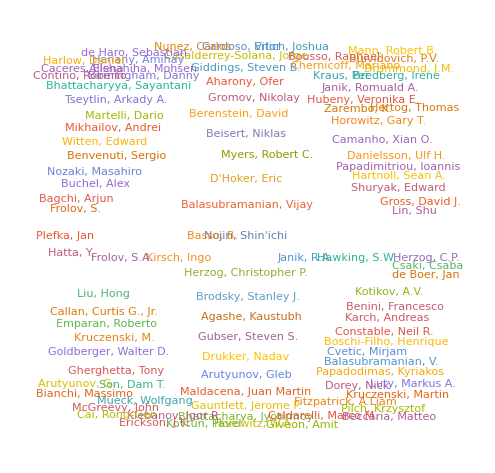

Data Sources Links/References

The database of record metadata has been downloaded from https://inspirehep.net/info/hep/api and the JSON file can be downloaded from https://inspirehep.net/hep_records.json.gz

Future Directions

It would be interesting for future works to study the mathematical properties of the citations graph and try to provide an additional bibliometric criterion to valuate scientific papers.

Background Info Links/References

Keywords

Provide keywords as items

word occurrence, search engine;

graph.

Other

A much more precise analysis should be carried out with a more detailed database. We noticed that roughly one-third of the records have no citations lists and/or abstracts.

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```

## Export notebook on Cloud

```mathematica
CopyFile[
"Desktop/RobertoOliveri_FP.nb",
CloudObject[
"RobertoOliveri_FP.nb",
Permissions->"Public"
]
]
```

CloudObject[https://www.wolframcloud.com/objects/user-cd1f147f-1b1f-420a-b028-659205f9c727/RobertoOliveri_FP.nb,Permissions→Public]